```mathematica
Off[Inverse::luc]
Off[LinearSolve::luc]

readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];

workingdirectory="/tmp/mul_helion-1";
SetDirectory[workingdirectory];

normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];{(Transpose[transf].DiagonalMatrix[μ^(-1/2)])}]

decompose[threshold_,norm_,ham_]:= Block[{},Oμ=normreg[threshold,norm][[1]];{λs,trf}=Eigensystem[(Transpose[Oμ].ham).Oμ];];
```

```mathematica
ℏc=197.32858;
Mnucl=(938.2796+939.5731)/2.;
histInput={};

DNormHamMat=readREAL8list["./MATOUTB"];

DBasisDim=IntegerPart[Sqrt[Length[DNormHamMat] 0.5]]
DNorm=ArrayReshape[DNormHamMat[[1;;DBasisDim^2]],{DBasisDim,DBasisDim}];
DHam=ArrayReshape[DNormHamMat[[DBasisDim^2+1;;]],{DBasisDim,DBasisDim}];
DNorm[[1;;12,1;;12]]//MatrixForm
DHam[[1;;12,1;;12]]//MatrixForm

evnbare=Sort[Eigenvalues[DNorm],#1>#2&];
Print["Norm EV_max = ",evnbare[[1]],"    Norm EV_min = ",evnbare[[-1]],"     Norm EV threshold = ",N[thr]];
thr=Max[10^-14,evnbare[[-1]]];
```

3098

(1. | 0.915524 | 0.655072 | 0.437574 | 0.294986 | 0.228279 | 0.126495 | 0.0783719 | 0.0558282 | 0.0346257 | 0.0245054 | 0.0100505
0.915524 | 1. | 0.873969 | 0.660763 | 0.48052 | 0.385276 | 0.225762 | 0.143892 | 0.103963 | 0.0654053 | 0.0466298 | 0.0193486
0.655072 | 0.873969 | 1. | 0.91948 | 0.763964 | 0.654553 | 0.428314 | 0.289536 | 0.215607 | 0.139909 | 0.10137 | 0.0431698
0.437574 | 0.660763 | 0.91948 | 1. | 0.945824 | 0.86903 | 0.644552 | 0.468174 | 0.362275 | 0.244792 | 0.181234 | 0.0799617
0.294986 | 0.48052 | 0.763964 | 0.945824 | 1. | 0.980283 | 0.824196 | 0.647174 | 0.523105 | 0.370684 | 0.281684 | 0.129851
0.228279 | 0.385276 | 0.654553 | 0.86903 | 0.980283 | 1. | 0.912692 | 0.756874 | 0.631571 | 0.463883 | 0.359686 | 0.171677
0.126495 | 0.225762 | 0.428314 | 0.644552 | 0.824196 | 0.912692 | 1. | 0.94729 | 0.858395 | 0.695082 | 0.57069 | 0.30195
0.0783719 | 0.143892 | 0.289536 | 0.468174 | 0.647174 | 0.756874 | 0.94729 | 1. | 0.974435 | 0.865151 | 0.752289 | 0.444478
0.0558282 | 0.103963 | 0.215607 | 0.362275 | 0.523105 | 0.631571 | 0.858395 | 0.974435 | 1. | 0.951767 | 0.866297 | 0.561955
0.0346257 | 0.0654053 | 0.139909 | 0.244792 | 0.370684 | 0.463883 | 0.695082 | 0.865151 | 0.951767 | 1. | 0.974992 | 0.735584
0.0245054 | 0.0466298 | 0.10137 | 0.181234 | 0.281684 | 0.359686 | 0.57069 | 0.752289 | 0.866297 | 0.974992 | 1. | 0.850902
0.0100505 | 0.0193486 | 0.0431698 | 0.0799617 | 0.129851 | 0.171677 | 0.30195 | 0.444478 | 0.561955 | 0.735584 | 0.850902 | 1.)

(1283.47 | 1118.25 | 769.682 | 504.378 | 336.463 | 259.165 | 142.597 | 88.0435 | 62.6112 | 38.7669 | 27.4126 | 11.2275
1118.25 | 1176.08 | 999.195 | 744.695 | 537.13 | 429.052 | 249.948 | 158.839 | 114.594 | 71.9874 | 51.2834 | 21.2539
769.682 | 999.195 | 1123.27 | 1023.7 | 845.93 | 722.86 | 470.937 | 317.599 | 236.216 | 153.09 | 110.848 | 47.1559
504.378 | 744.695 | 1023.7 | 1107.09 | 1043.34 | 956.837 | 707.327 | 512.784 | 396.384 | 267.545 | 197.961 | 87.2562
336.463 | 537.13 | 845.93 | 1043.34 | 1100.42 | 1077.31 | 903.521 | 708.358 | 572.055 | 404.976 | 307.577 | 141.657
259.165 | 429.052 | 722.86 | 956.837 | 1077.31 | 1097.85 | 999.962 | 828.138 | 690.495 | 506.712 | 392.697 | 187.269
142.597 | 249.948 | 470.937 | 707.327 | 903.521 | 999.962 | 1094.3 | 1035.7 | 937.981 | 759.006 | 622.918 | 329.331
88.0435 | 158.839 | 317.599 | 512.784 | 708.358 | 828.138 | 1035.7 | 1092.68 | 1064.32 | 944.461 | 820.979 | 484.743
62.6112 | 114.594 | 236.216 | 396.384 | 572.055 | 690.495 | 937.981 | 1064.32 | 1091.91 | 1038.81 | 945.262 | 612.826
38.7669 | 71.9874 | 153.09 | 267.545 | 404.976 | 506.712 | 759.006 | 944.461 | 1038.81 | 1091.14 | 1063.64 | 802.101
27.4126 | 51.2834 | 110.848 | 197.961 | 307.577 | 392.697 | 622.918 | 820.979 | 945.262 | 1063.64 | 1090.76 | 927.782
11.2275 | 21.2539 | 47.1559 | 87.2562 | 141.657 | 187.269 | 329.331 | 484.743 | 612.826 | 802.101 | 927.782 | 1090.14)

Norm EV_max = 165.609    Norm EV_min = -1.10274×10^-15     Norm EV threshold = thr

```mathematica
decompose[thr,DNorm,DHam];
evhamunnorm=Sort[Eigenvalues[{DHam,DNorm}],Re[#1]>Re[#2]&];
```

Condition number ℕ_ij = 1.5018×10^17

EV_full(ℍ) = {-2.07121+0. ⅈ,-2.49575+0. ⅈ,-11.6356+0. ⅈ,-395.369+0. ⅈ}

EV_(EV (𝟙) > threshold)(ℍ) = {-1.9472+0. ⅈ,-2.00723+0. ⅈ,-2.04676+0. ⅈ,-2.07121+0. ⅈ}

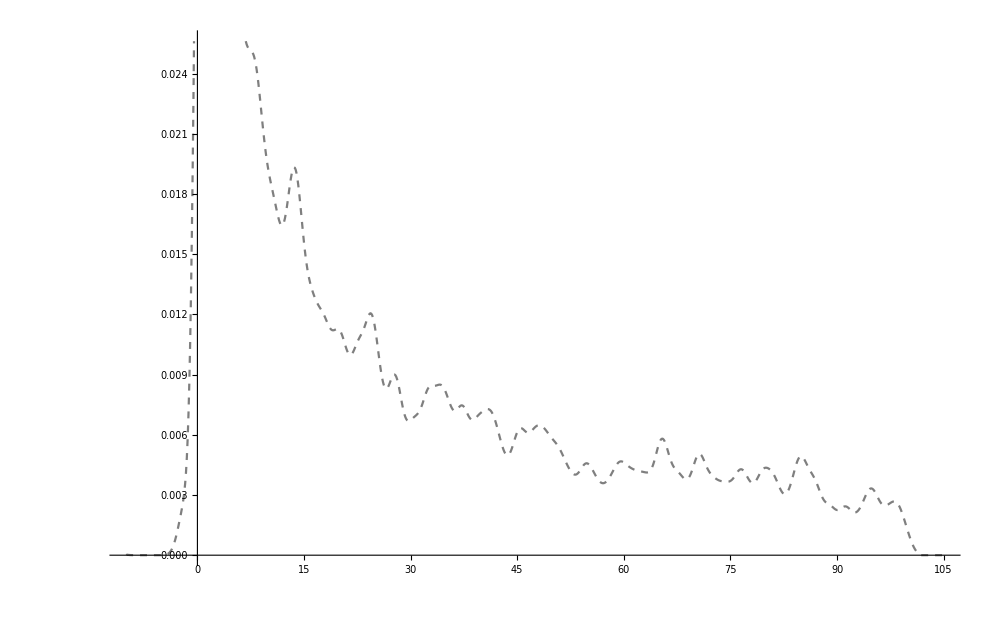

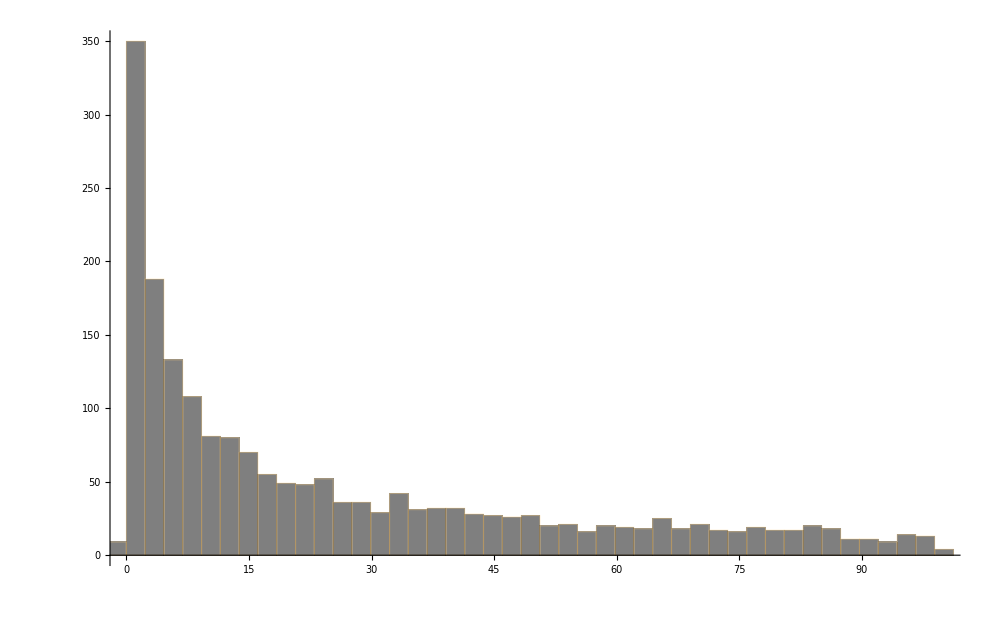

```mathematica
renorm=DiagonalMatrix[1/Sqrt[Diagonal[DNorm]]];
renormid=DiagonalMatrix[Table[1,{n,DBasisDim}]];
DHam=renorm.DHam.renorm;DNorm=renorm.DNorm.renorm;
evhamnorm=Sort[Eigenvalues[{DHam,DNorm}],Re[#1]>Re[#2]&];

evn=Eigenvalues[DNorm];

Print["Condition number ℕ_ij = ",Abs[Max[evn]/Min[evn]]];
Print["EV_full(ℍ) = ",evhamnorm[[-4;;]]];
Print["EV_(EV (𝟙) > threshold)(ℍ) = ",Sort[λs,Re[#1]>Re[#2]&][[-4;;]]];

thh=100;
AppendTo[histInput,{Select[Re[evhamunnorm],Abs[#]<thh&],Re[Select[evhamnorm,Abs[#1]<thh&]]}];


histInput[[1,All]];
SmoothHistogram[histInput[[All,1]],0.8,ImageSize->1000,PlotRange->{{-10,1.05 thh},Automatic},PlotStyle->{{Black,Dashed,Thick,Opacity[0.5]},Blue,Orange}]
Histogram[histInput[[All,1]],{2.3},ImageSize->1000,PlotRange->{{0,thh},Automatic},ChartStyle->{Black,Blue,Orange}]
```